```mathematica
VarMix =ParallelTable[
Var=
{ Table[
n=10;
mu = RandomVariate[NormalDistribution[-15,0.5],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
 Table[
n=10;
mu = RandomVariate[NormalDistribution[-15,1],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}]},
(*{x,Mean[Var]},*)
{x,0.1,2,0.1}];
```

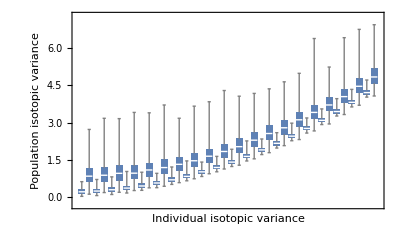

```mathematica
IndPopVarPlot=BoxWhiskerChart[VarMix,ChartStyle->ColorData[97,1],(*ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],*)
FrameLabel->{"Individual isotopic variance","Population isotopic variance"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf",IndPopVarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf

```mathematica
VarMix1 =ParallelTable[
Var=
 Table[
n=50;
mu = RandomVariate[NormalDistribution[-15,0.5],n];
var = Table[x,{n}];(1/n^2)*(Sum[n*var[[i]] + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
(*{x,Mean[Var]},*)
{x,0.1,2,0.05}];
VarMix2 =ParallelTable[
Var=Table[
n=50;
mu = RandomVariate[NormalDistribution[-15,2],n];
var = Table[x,{n}];(1/n^2)*(Sum[n*var[[i]] + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,1000}],
(*{x,Mean[Var]},*)
{x,0.1,2,0.05}];
```

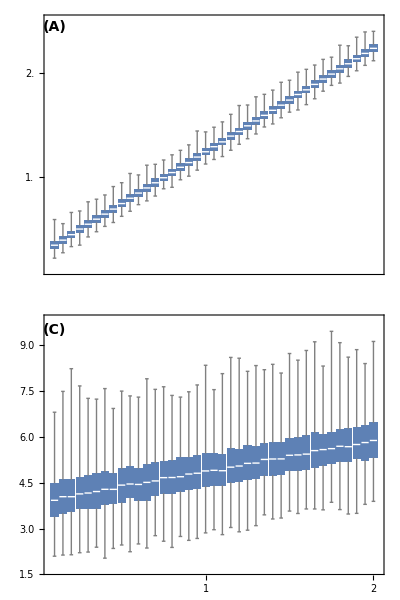
-Graphics-Population isotopic varianceIndividual isotopic variance

```mathematica
IndPopVarPlot2=
Labeled[Column[{
Show[{
BoxWhiskerChart[VarMix1,ChartStyle->ColorData[97,1],(*ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],*)
ImageSize->300,FrameTicks->{Automatic,Table[x,{x,0,5,0.5}],None,None}],
Graphics[Text[Style["(A)",Bold,FontSize->14],{1,2.45}]]
}],
Show[{
IndPopVarPlot=BoxWhiskerChart[VarMix2,ChartStyle->ColorData[97,1],ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],
ImageSize->300],
Graphics[Text[Style["(C)",Bold,FontSize->14],{1,9.50}]]
}]
},Spacings->-0.25],
TraditionalForm/@{Rotate["Population δ^13C variance",90Degree],"Individual δ^13C variance"},{Left,Bottom},Spacings->{1,0},LabelStyle->"Panel"]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf",IndPopVarPlot2]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf

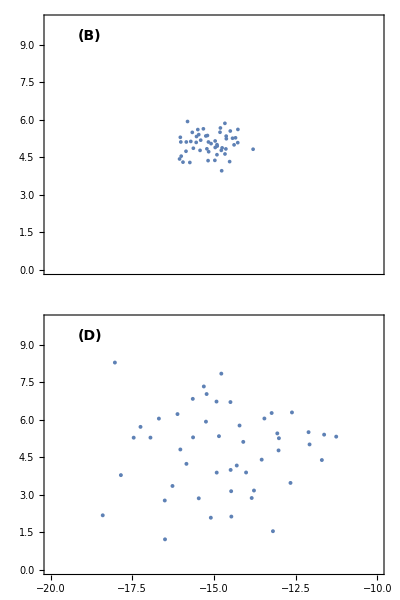
-Graphics-δ^15Nδ^13C

```mathematica
n=50;
mu1 = RandomVariate[NormalDistribution[-15,0.5],n];
mu2 = RandomVariate[NormalDistribution[5,0.5],n];
mu21 = RandomVariate[NormalDistribution[-15,2],n];
mu22 = RandomVariate[NormalDistribution[5,2],n];
DistPlot =
Labeled[Column[{
Show[{
ListPlot[Transpose[{mu1,mu2}],Frame->True,PlotRange->{{-20,-10},{0,10}},ImageSize->160,AspectRatio->1.2,FrameTicks->{None,Automatic,Automatic,Automatic}],
Graphics[Text[Style["(B)",Bold,FontSize->14],{-18.8,9.35}]]
}],
Show[{
ListPlot[Transpose[{mu21,mu22}],Frame->True,PlotRange->{{-20,-10},{0,10}},ImageSize->168,AspectRatio->1.2],
Graphics[Text[Style["(D)",Bold,FontSize->14],{-18.8,9.35}]]
}]
},Spacings->-0.45],
TraditionalForm/@{Rotate["δ^15N",90Degree],"δ^13C"},{Left,Bottom},Spacings->{0.5,0},LabelStyle->"Panel"]
```

```mathematica
InpPopDist = Row[{
IndPopVarPlot2,
DistPlot
},"  "]
```

-Graphics-Population isotopic varianceIndividual isotopic variance-Graphics-δ^15Nδ^13C

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf",InpPopDist]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar2.pdf